```mathematica
D[BesselJ[n,x],x]
```

1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x])

```mathematica
D[HankelH2[n,x],x]
```

1/2 (HankelH2[-1+n,x]-HankelH2[1+n,x])

```mathematica
Jp[n_,x_]:=Evaluate[D[BesselJ[n,x],x]]
H2p[n_,x_]:=Evaluate[D[HankelH2[n,x],x]]
```

```mathematica
Plot[f[1,x],{x,0,10}]
```

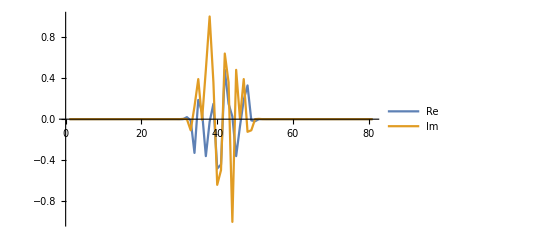

```mathematica
bn=Table[N[-I^(-n) Jp[n,2Pi]/H2p[n,2Pi]],{n,-40,40}];
ListPlot[{Re[bn],Im[bn]},PlotRange->All, Joined->True,PlotLegends->{"Re","Im"}]
```